```mathematica
sampling = 524288;
amplitude = Floor[(Power[2,16]-1)/4]
```

16383

```mathematica
c=34000;
```

```mathematica
recSampling=48000;
```

```mathematica
Power[2,16]
```

65536

```mathematica
Clear[freq] ;
freq = {};
For[i=1,i≤6,i++,
AppendTo[freq,{14000 + i*1000-250, 14000+i*1000+250}];
]
```

```mathematica
freq
```

{{14750,15250},{15750,16250},{16750,17250},{17750,18250},{18750,19250},{19750,20250}}

```mathematica
SyncPattern[t_,freq1_,freq2_,ψ_,θ_]:=Sin[freq1 2Pi t + ψ] + Sin[freq2 2Pi t + ψ + θ];
```

```mathematica
(*数値計算用、データリスト*)
Clear[sync];
sync ={};
Clear[ComSin];
ComSin = {};
For[i=1,i≤Length[freq],i++,
Clear[tmp];
tmp={};
For[j=1,j≤Length[freq[[i]]],j++,
AppendTo[tmp,Table[Exp[-ⅉ 2Pi freq[[i,j]] t],{t,-1/1000,1/1000,1/recSampling}]//N];
];
AppendTo[ComSin,tmp];
AppendTo[sync,Table[SyncPattern[t,freq[[i,1]],freq[[i,2]],0,0],{t,-1/1000,3/1000,1/recSampling}]//N];
]
```

```mathematica
comSampling = sampling/2;
```

```mathematica
M=6;
SymNum=10;
```

```mathematica
g[n_]:=
If[n==0,0,
If[Mod[n,2]==1,Ceiling[SymNum/2],-(Ceiling[SymNum/2]-1)]
];
```

```mathematica
Clear[ψ];
ψ={};
sum=0;
For[i=1,i≤SymNum,i++,
sum+=g[i-1];
AppendTo[ψ,2Pi sum/SymNum];
]
```

```mathematica
Clear[θ];
θ={};
For[i=1,i≤SymNum,i++,
AppendTo[θ,Mod[(i-1)Pi/3,2Pi]];
]
```

```mathematica
Subscript[f, 0]=12000;
Subscript[f, 1]=18000;
k=(Subscript[f, 1]-Subscript[f, 0])/10/1000//N;
```

```mathematica
ChirpSignal[t_]:=Sin[2Pi(Subscript[f, 0] + t k/2 )t]//N;
```

```mathematica
chirp=Table[ChirpSignal[t],{t,0/1000,10/1000,1/comSampling}];
```

```mathematica
chirp48=Table[ChirpSignal[t],{t,0,10/1000,1/recSampling}];
```

```mathematica
Clear[pilot];
pilot={};
AppendTo[pilot,Table[If[t≥3/1000&&t≤13/1000,2amplitude ChirpSignal[t-3/1000]//N,0],{t,0,150/1000-1/comSampling,1/comSampling}]];
For[i=1,i≤3,i++,
AppendTo[pilot,Table[0.,{t,comSampling*150/1000 - 1/comSampling}]];
Length[pilot[[i+1]]]
]
```

```mathematica
amplitude
```

16383

```mathematica
amplitude2={amplitude/2,amplitude,amplitude/2,amplitude}//N;
```

```mathematica
(*Clear[SpotWave];
SpotWave={};
For[j=1,j≤4,j++,
Clear[tmp];
tmp=pilot[[j]];
For[i=1,i≤SymNum,i++,
tmp=Join[tmp,
Table[
If[Mod[1000t,150]>3 -θ[[i]]/Pi-1000ts[[j]](*+50(j+Mod[j,2]-2)/2*)&&Mod[1000t,150]<7-θ[[i]]/Pi-1000ts[[j]](*+50(j+Mod[j,2]-2)/2*),
amplitude2[[j]] SyncPattern[t+ts[[j]],freq[[(j+Mod[j,2])/2+4,1]],freq[[(j+Mod[j,2])/2+4,2]],ψ[[i]]*Mod[j,2],θ[[i]]],0]//N,
{t,(i-1)*150/1000,i*150/1000-1/comSampling,1/comSampling}
]
]
];
AppendTo[SpotWave,tmp];
]
For[i=1,i≤Length[SpotWave],i++,
SpotWave[[i]]=Join[SpotWave[[i]],Table[0.,{t,2 comSampling-Length[SpotWave[[i]]]}]];
]
SetDirectory["C:\\Users\\Shoma\\Documents\\Wolfram Mathematica\\output"];
Export["spot1_250-250.txt",SpotWave[[1]]];
Export["spot2_250-250.txt",SpotWave[[2]]];
Export["spot3_250-250.txt",SpotWave[[3]]];
Export["spot4_250-250.txt",SpotWave[[4]]];*)
```

```mathematica
(*ListLinePlot[SpotWave[[1]],PlotRange->All]
ListLinePlot[SpotWave[[2]],PlotRange->All]
ListLinePlot[SpotWave[[3]],PlotRange->All]
ListLinePlot[SpotWave[[4]],PlotRange->All]*)
```

```mathematica
(*Animate[ListLinePlot[SpotWave[[1,1+(index-1)Ceiling[comSampling*150/1000];;(index-1)Ceiling[comSampling*150/1000]+3000]],PlotRange->All],{index,1,10,1}]
Animate[ListLinePlot[SpotWave[[2,1+(index-1)Ceiling[comSampling*150/1000];;(index-1)Ceiling[comSampling*150/1000]+3000]],PlotRange->All],{index,1,10,1}]
Animate[ListLinePlot[SpotWave[[3,1+(index-1)Ceiling[comSampling*150/1000];;(index-1)Ceiling[comSampling*150/1000]+3000]],PlotRange->All],{index,1,10,1}]
Animate[ListLinePlot[SpotWave[[4,1+(index-1)Ceiling[comSampling*150/1000];;(index-1)Ceiling[comSampling*150/1000]+3000]],PlotRange->All],{index,1,10,1}]*)
```

```mathematica
i=1
```

1

```mathematica
posi = {"center","right","left"};
Clear[rawComData];
rawComData={};
Clear[tmp];
tmp = {};
SetDirectory["/home/yshoma/develop/workspace/octave/20190710/"]
For[i=1,i≤3,i++,
For[j = 1,j ≤ 2,j++,
AppendTo[tmp,Import[posi[[i]]<>"_0"<>ToString[j]<>".wav","Data"][[1]]];
Print["/home/yshoma/develop/workspace/octave/20190710/"<>posi[[i]]<>"_0"<>ToString[j]<>".wav"];
Print[Length[tmp]];
];
];
AppendTo[rawComData,tmp];
```

/home/yshoma/develop/workspace/octave/20190710

/home/yshoma/develop/workspace/octave/20190710/center_01.wav

1

/home/yshoma/develop/workspace/octave/20190710/center_02.wav

2

/home/yshoma/develop/workspace/octave/20190710/right_01.wav

3

/home/yshoma/develop/workspace/octave/20190710/right_02.wav

4

/home/yshoma/develop/workspace/octave/20190710/left_01.wav

5

/home/yshoma/develop/workspace/octave/20190710/left_02.wav

6

```mathematica
Length[rawComData]
Length[rawComData[[1]]]
Length[rawComData[[1,1]]]
```

1

6

10574400

```mathematica
Clear[comData];
comData={};
For[i=1,i≤Length[rawComData],i++,
Clear[tmp];
tmp={};
For[j=1,j≤Length[rawComData[[i]]],j++,
AppendTo[tmp,rawComData[[i,j,recSampling*8;;recSampling*212]]];
];
AppendTo[comData,tmp];
]
```

```mathematica
TimeA=AbsoluteTime[];
Clear[demoduled];
demoduled={};
time1 = AbsoluteTime[];
For[iterSpotNum=1,iterSpotNum≤Length[comData],iterSpotNum++,
Clear[tmpDemRecNum];
tmpDemRecNum={};
For[iterRecNum=1,iterRecNum≤Length[comData[[iterSpotNum]]],iterRecNum++,
Print[{iterSpotNum,iterRecNum}];
Clear[tmpDemoduled];
tmpDemoduled={};
index = 0;
For[i=1,i≤100,i++,
If[Mod[i,25]==0,
time2 = AbsoluteTime[];
Print[{i,time2 - time1}];
time1 = time2;
];
index += recSampling + Ordering[ListCorrelate[chirp48,comData[[iterSpotNum,iterRecNum,index+recSampling;;index+3 recSampling]]],-1][[1]];
index +=151 recSampling/1000;
arg1=Arg[2ⅉ ListCorrelate[ComSin[[5,2]],comData[[iterSpotNum,iterRecNum,index;;index+2recSampling/1000]]]]-Arg[2ⅉ ListCorrelate[ComSin[[5,1]],comData[[iterSpotNum,iterRecNum,index;;index+2 recSampling/1000]]]]+Pi;
arg2=Arg[2ⅉ ListCorrelate[ComSin[[6,2]],comData[[iterSpotNum,iterRecNum,index;;index+2 recSampling/1000]]]]-Arg[2ⅉ ListCorrelate[ComSin[[6,1]],comData[[iterSpotNum,iterRecNum,index;;index+2 recSampling/1000]]]]+Pi;
If[arg1>Pi,
arg1-= 2Pi,
If[arg1≤ -Pi,
arg1+=2Pi]
];
If[arg2>Pi,
arg2-= 2Pi,
If[arg2≤ -Pi,
arg2+=2Pi]
];
(*epoch1=Round[index+48(arg1/Abs[arg1]-arg1/Pi)[[1]]]-48;
epoch2=Round[index+48(arg2/Abs[arg2]-arg2/Pi)[[1]]]-48;*)
epoch1 = index-48;
epoch2 = index-48;
prearg1=arg1;
prearg2=arg2;
Clear[Arg1];
Clear[Arg2];
Arg1={};
Arg2={};
For[j=1,j≤9,j++,
arg1=(Arg[2ⅉ ListCorrelate[ComSin[[5,2]],comData[[iterSpotNum,iterRecNum,epoch1+j 150 recSampling/1000;;epoch1+(2+j 150)recSampling/1000]]]]-Arg[2ⅉ ListCorrelate[ComSin[[5,1]],comData[[iterSpotNum,iterRecNum,epoch1+j 150 recSampling/1000;;epoch1+(2+j 150)recSampling/1000]]]])[[1]];
arg2=(Arg[2ⅉ ListCorrelate[ComSin[[6,2]],comData[[iterSpotNum,iterRecNum,epoch2+j 150 recSampling/1000;;epoch2+(2+j 150)recSampling/1000]]]]-Arg[2ⅉ ListCorrelate[ComSin[[6,1]],comData[[iterSpotNum,iterRecNum,epoch2+j 150 recSampling/1000;;epoch2+(2+j 150)recSampling/1000]]]])[[1]];
If[arg1>Pi,
arg1-= 2Pi,
If[arg1≤ -Pi,
arg1+=2Pi
]
];
If[arg2>Pi,
arg2-= 2Pi,
If[arg2≤ -Pi,
arg2+=2Pi
]
];
tmp1=arg1-prearg1;
If[tmp1>Pi,
tmp1-=2Pi,
If[tmp1≤-Pi,
tmp1+=2Pi
]
];
tmp2=arg2-prearg2;
If[tmp2>Pi,
tmp2-=2Pi,
If[tmp2≤-Pi,
tmp2+=2Pi
]
];
If[tmp1≥-Pi&&tmp1<-5Pi/6,
tmp1=-Pi,
If[tmp1≥-5Pi/6&&tmp1<-3Pi/6,
tmp1=-2Pi/3,
If[tmp1≥-3Pi/6&&tmp1<-Pi/6,
tmp1=-Pi/3,
If[tmp1≥-Pi/6&&tmp1<Pi/6,
tmp1=0,
If[tmp1≥Pi/6&&tmp1<3Pi/6,
tmp1=Pi/3,
If[tmp≥3Pi/6&&tmp1<5Pi/6,
tmp1=2Pi/3,
0
]
]
]
]
]
];
If[tmp2≥-Pi&&tmp2<-5Pi/6,
tmp2=-Pi,
If[tmp2≥-5Pi/6&&tmp2<-3Pi/6,
tmp2=-2Pi/3,
If[tmp2≥-3Pi/6&&tmp2<-Pi/6,
tmp2=-Pi/3,
If[tmp2≥-Pi/6&&tmp2<Pi/6,
tmp2=0,
If[tmp2≥Pi/6&&tmp2<3Pi/6,
tmp2=Pi/3,
If[tmp≥3Pi/6&&tmp2<5Pi/6,
tmp2=2Pi/3,
0
]
]
]
]
]
];
AppendTo[Arg1,tmp1];
AppendTo[Arg2,tmp2];
prearg1=arg1;
prearg2=arg2;
];
AppendTo[tmpDemoduled,{Arg1,Arg2}];
];
AppendTo[tmpDemRecNum,tmpDemoduled];
];
AppendTo[demoduled,tmpDemRecNum];
];
TimeB=AbsoluteTime[];
Print[TimeB-TimeA];
```

{1,1}

{25,0.043838}

{50,0.037898}

{75,36.290076}

{100,8.510954}

{1,2}

{25,4.279086}

{50,5.758092}

{75,4.283206}

{100,9.993298}

{1,3}

{25,67.764917}

{50,66.336391}

{75,67.723323}

{100,77.532692}

{1,4}

{25,14.17444}

{50,12.73337}

{75,23.23197}

{100,23.3767}

{1,5}

{25,30.44359}

{50,27.9927}

{75,28.39779}

{100,27.52103}

{1,6}

{25,7.217607}

{50,0.038653}

{75,5.754064}

{100,2.89955}

552.337447

```mathematica
161986-65986
```

96000

```mathematica
Length[demoduled]
```

1

```mathematica
Pi 2/3//N
```

2.0944

```mathematica
demoduled[[1,1,1]]
```

{{{-10.2448},0,0,0,π/3,-(2 π)/3,0,0,0},{{-9.47334},0,0,-π/3,0,π/3,0,0,0}}

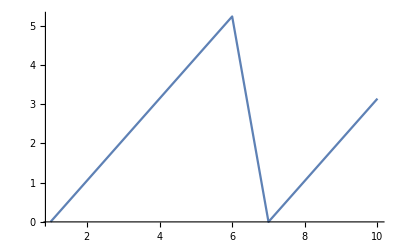

```mathematica
ListLinePlot[θ,PlotRange->All]
```

```mathematica
reference=θ[[2;;]]-θ[[;;-2]];
For[i=1,i≤Length[reference],i++,
If[reference[[i]]>Pi,
reference[[i]]-=2Pi,
If[reference[[i]]≤-Pi,
reference[[i]]+=2Pi]
];
];
```

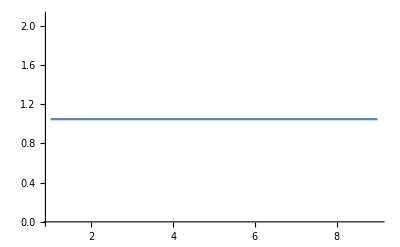

```mathematica
ListLinePlot[reference,PlotRange->All]
```

```mathematica
reference[[1]]==demoduled[[1,1,1,1,1]]
```

π/3=={-10.2448}

```mathematica
Clear[result];
result={};
For[i=1,i≤Length[demoduled],i++,
Clear[tmp1];
tmp1={};
For[j=1,j≤Length[demoduled[[i]]],j++,
Clear[tmp2];
tmp2={{},{}};
For[k=1,k≤Length[demoduled[[i,j]]],k++,(*100回繰り返す*)
For[l=1,l≤Length[demoduled[[i,j,k]]],l++,(*α,βの二回*)
eval=9;
For[m=1,m≤Length[demoduled[[i,j,k,l]]],m++,(*ここで、9回繰り返す*)
If[demoduled[[i,j,k,l,m]]== reference[[m]],eval--];
];
AppendTo[tmp2[[l]],eval];
]
(*AppendTo[tmp2,tmp3];*)
];
AppendTo[tmp1,tmp2];
];
AppendTo[result,tmp1];
];
```

```mathematica
Length[result]
Length[result[[1,1,1]]]
```

1

100

```mathematica
result[[1,2,1]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1}

```mathematica
Clear[count];
count={{},{}};
For[i=1,i≤Length[result],i++,
Clear[tmp1];
tmp1={};
Clear[tmp2];
tmp2={};
For[j=1,j≤Length[result[[i]]],j++,
AppendTo[tmp1,Count[result[[i,j,1]],0]];
AppendTo[tmp2,Count[result[[i,j,2]],0]];
];
AppendTo[count[[1]],tmp1];
AppendTo[count[[2]],tmp2];
]
```

```mathematica
count
```

{{{0,0,0,0,0,0}},{{0,0,0,0,0,0}}}

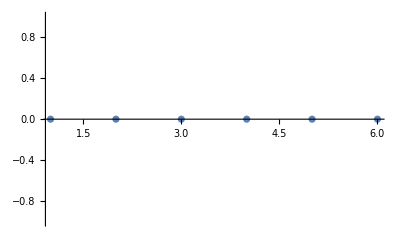

-Graphics-

```mathematica
ListPlot[count[[1]],PlotRange->All]
ListPlot[count[[2]],PlotRange->All]
```

```mathematica
Count[result[[1,1,1]],0]
```

0

```mathematica
Length[result[[1,1,1]]]
```

100